```mathematica
(*this was my previous attempt, it uses the wrong fundamental contribution

Nf=1;
BA1[σ1_,σ2_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]-σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]-σ2] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ2],{i,1,Nf}];
(BA1[σ1+1,σ2]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1+1,σ2-1])//Simplify

*)
```

-(1+σ1-σ2)^2

```mathematica
(******************)

(*the correct one seems to be (∏^Nf)_(i=1) G(1+Subscript[m, i]+Subscript[σ, 1])G(1+Subscript[m, i]+Subscript[σ, 2])   *)
```

```mathematica
Nf=1;
Ns=0;
Nadj = 0;
Table[
instno=k;
tableaux=Flatten[Table[If[k1+k2+k3==instno,Table[{Y1,Y2,Y3},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]},{Y3,IntegerPartitions[k3]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]},{k3,Range[0,instno]}],5];
Subscript[Z, k]=Sum[Product[(((ToExpression[StringJoin["madj",ToString[i]]]-e1)(ToExpression[StringJoin["madj",ToString[i]]]-e2))/(ToExpression[StringJoin["madj",ToString[i]]](ToExpression[StringJoin["madj",ToString[i]]]-e1-e2)))^1 Product[Product[((ϕ[σ1,cell[[1]],cell[[2]]]-ToExpression[StringJoin["σ",ToString[j]]])^2-(ToExpression[StringJoin["madj",ToString[i]]]-e1-e2)^2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[Product[((ϕ[σ2,cell[[1]],cell[[2]]]-ToExpression[StringJoin["σ",ToString[j]]])^2-(ToExpression[StringJoin["madj",ToString[i]]]-e1-e2)^2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}]Product[Product[((ϕ[σ3,cell[[1]],cell[[2]]]-ToExpression[StringJoin["σ",ToString[j]]])^2-(ToExpression[StringJoin["madj",ToString[i]]]-e1-e2)^2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[3]]][[rowno]]}],{rowno,1,Length[Range[Y[[3]]]]}],1]}],{i,1,Nadj}]Product[Product[(2ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e1)(2ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e2)Product[(ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]+ToExpression[StringJoin["σ",ToString[j]]]-e1-e2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[(2ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e1)(2ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e2)Product[(ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]+ToExpression[StringJoin["σ",ToString[j]]]-e1-e2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}]Product[(2ϕ[σ3,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e1)(2ϕ[σ3,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]-e2)Product[(ϕ[σ3,cell[[1]],cell[[2]]]+ToExpression[StringJoin["ms",ToString[i]]]+ToExpression[StringJoin["σ",ToString[j]]]-e1-e2),{j,1,3}],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[3]]][[rowno]]}],{rowno,1,Length[Range[Y[[3]]]]}],1]}],{i,1,Ns}]Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["mf",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["mf",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}]Product[ϕ[σ3,cell[[1]],cell[[2]]]+ToExpression[StringJoin["mf",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[3]]][[rowno]]}],{rowno,1,Length[Range[Y[[3]]]]}],1]}],{i,1,Nf}]/(Product[ξ12[ToExpression[StringJoin["σ",ToString[i]]],ToExpression[StringJoin["σ",ToString[j]]],Y[[i]],Y[[j]]],{i,1,3},{j,1,3}])//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}//Simplify,{k,0,2}]//Simplify
```

{1,-(σ1^2 (σ2+σ3)+σ2 σ3 (σ2+σ3)+σ1 (σ2^2-6 σ2 σ3+σ3^2)+2 mf1 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2),1/4 (((mf1+σ1) (1+mf1+σ1))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2)+(4 (mf1+σ1) (mf1+σ2))/((1+σ1-σ2)^2 (1-σ1+σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)+((mf1+σ2) (1+mf1+σ2))/((σ1-σ2)^2 (1-σ1+σ2)^2 (σ2-σ3)^2 (1+σ2-σ3)^2)+((-1+mf1+σ3) (mf1+σ3))/((σ1-σ3)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1+σ2-σ3)^2)+((-1+mf1+σ1) (mf1+σ1))/((σ1-σ2)^2 (1-σ1+σ2)^2 (σ1-σ3)^2 (1-σ1+σ3)^2)+(4 (mf1+σ1) (mf1+σ3))/((σ1-σ2)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1-σ1+σ3)^2)+((-1+mf1+σ2) (mf1+σ2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ2-σ3)^2 (1-σ2+σ3)^2)+(4 (mf1+σ2) (mf1+σ3))/((σ1-σ2)^2 (σ1-σ3)^2 (1+σ2-σ3)^2 (1-σ2+σ3)^2)+((mf1+σ3) (1+mf1+σ3))/((σ1-σ3)^2 (σ2-σ3)^2 (1-σ1+σ3)^2 (1-σ2+σ3)^2))}

```mathematica
Ns=0;
Nas=0;
Nf=1;
Nadj=2;
BA2[σ1_,σ2_,σ3_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]G[1+σ1-σ3] G[1-σ1+σ3]G[1+σ2-σ3] G[1-σ2+σ3]) Product[G[1+ToExpression[StringJoin["mas",ToString[i]]]+{σ1,σ2,σ3}.a]  ,{i,1,Nas},{a,{{1,1,0},{0,1,1},{1,0,1}}}]Product[G[1+ToExpression[StringJoin["mf",ToString[i]]]+{σ1,σ2,σ3}.a]  ,{i,1,Nf},{a,{{1,0,0},{0,1,0},{0,0,1}}}]Product[G[1+ToExpression[StringJoin["ms",ToString[i]]]+{σ1,σ2,σ3}.a]  ,{i,1,Ns},{a,{{2,0,0},{1,1,0},{0,2,0},{1,0,1},{0,1,1},{0,0,2}}}]Product[G[1+ToExpression[StringJoin["madj",ToString[i]]]+{σ1,σ2,σ3}.a]  ,{i,1,Nadj},{a,{{1,0,-1},{0,1,-1},{1,-1,0},{0,0,0},{0,0,0},{-1,1,0},{0,-1,1},{-1,0,1}}}];

(BA2[σ1+1,σ2,σ3]BA2[σ1,σ2-1,σ3])/(BA2[σ1,σ2,σ3]BA2[σ1+1,σ2-1,σ3])//Simplify

Z1loop=-((BA2[σ1+1,σ2,σ3]BA2[σ1-1,σ2,σ3])/BA2[σ1,σ2,σ3]^2+(BA2[σ1,σ2+1,σ3]BA2[σ1,σ2-1,σ3])/BA2[σ1,σ2,σ3]^2+(BA2[σ1,σ2,σ3+1]BA2[σ1,σ2,σ3-1])/BA2[σ1,σ2,σ3]^2)//Simplify;
Subscript[Z, 1]/Z1loop //Simplify
Z2loop=-1/4((BA2[σ1+1,σ2,σ3]BA2[σ1-1,σ2,σ3])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])((Z1loop/.{σ1->σ1+1})+(Z1loop/.{σ1->σ1-1}))+(BA2[σ1,σ2+1,σ3]BA2[σ1,σ2-1,σ3])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])((Z1loop/.{σ2->σ2+1})+(Z1loop/.{σ2->σ2-1}))+(BA2[σ1,σ2,σ3+1]BA2[σ1,σ2,σ3-1])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])((Z1loop/.{σ3->σ3+1})+(Z1loop/.{σ3->σ3-1})))-((σ1-σ2)^2/((madj1+σ1-σ2) (madj1-σ1+σ2)))^1(BA2[σ1+1,σ2-1,σ3]BA2[σ1-1,σ2+1,σ3])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])-((σ1-σ3)^2/((madj1+σ1-σ3) (madj1-σ1+σ3)))^1(BA2[σ1+1,σ2,σ3-1]BA2[σ1-1,σ2,σ3+1])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])-((σ2-σ3)^2/((madj1+σ2-σ3) (madj1-σ2+σ3)))^1(BA2[σ1,σ2+1,σ3-1]BA2[σ1,σ2-1,σ3+1])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])//Simplify;
Subscript[Z, 2]/Z2loop//Simplify
```

-(1+σ1-σ2)^2/((1+madj1+σ1-σ2) (-1+madj1-σ1+σ2))

1-madj1^2

((1-madj1) (1+madj1) (σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1+σ2-σ3)^2 (1-σ1+σ3)^2 (1-σ2+σ3)^2 (-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1+σ1-σ2)^2) (madj1^2-(σ1-σ3)^2) (madj1^2-(1+σ1-σ3)^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2)-(4 madj1^2 (madj1^2-(σ1-σ2)^2)^2 (madj1^2-(σ1-σ3)^2) (madj1^2-(σ2-σ3)^2))/((1+σ1-σ2)^2 (1-σ1+σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1-σ1+σ2)^2) (madj1^2-(σ2-σ3)^2) (madj1^2-(1+σ2-σ3)^2))/((σ1-σ2)^2 (1-σ1+σ2)^2 (σ2-σ3)^2 (1+σ2-σ3)^2)-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ3)^2) (madj1^2-(1+σ1-σ3)^2) (madj1^2-(σ2-σ3)^2) (madj1^2-(1+σ2-σ3)^2))/((σ1-σ3)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1+σ2-σ3)^2)-(4 madj1^2 (madj1^2-(σ1-σ2)^2) (madj1^2-(σ1-σ3)^2)^2 (madj1^2-(σ2-σ3)^2))/((σ1-σ2)^2 (1+σ1-σ3)^2 (σ2-σ3)^2 (1-σ1+σ3)^2)-(4 madj1^2 (madj1^2-(σ1-σ2)^2) (madj1^2-(σ1-σ3)^2) (madj1^2-(σ2-σ3)^2)^2)/((σ1-σ2)^2 (σ1-σ3)^2 (1+σ2-σ3)^2 (1-σ2+σ3)^2)-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1-σ1+σ2)^2) (madj1^2-(σ1-σ3)^2) (madj1^2-(1-σ1+σ3)^2))/((σ1-σ2)^2 (1-σ1+σ2)^2 (σ1-σ3)^2 (1-σ1+σ3)^2)-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1+σ1-σ2)^2) (madj1^2-(σ2-σ3)^2) (madj1^2-(1-σ2+σ3)^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ2-σ3)^2 (1-σ2+σ3)^2)-((-1+madj1) (1+madj1) (madj1^2-(σ1-σ3)^2) (madj1^2-(σ2-σ3)^2) (madj1^2-(1-σ1+σ3)^2) (madj1^2-(1-σ2+σ3)^2))/((σ1-σ3)^2 (σ2-σ3)^2 (1-σ1+σ3)^2 (1-σ2+σ3)^2)))/(-4 (-1+madj1+σ1-σ2) (madj1+σ1-σ2) (1+madj1+σ1-σ2) (-1+madj1-σ1+σ2) (madj1-σ1+σ2) (1+madj1-σ1+σ2) (1+σ1-σ3)^2 (madj1+σ1-σ3) (1+σ2-σ3)^2 (madj1+σ2-σ3) (1-σ1+σ3)^2 (madj1-σ1+σ3) (1-σ2+σ3)^2 (madj1-σ2+σ3)-4 (1+σ1-σ2)^2 (madj1+σ1-σ2) (1-σ1+σ2)^2 (madj1-σ1+σ2) (1-madj1+σ1-σ3) (madj1+σ1-σ3) (1+madj1+σ1-σ3) (1+σ2-σ3)^2 (madj1+σ2-σ3) (1-madj1-σ1+σ3) (madj1-σ1+σ3) (1+madj1-σ1+σ3) (1-σ2+σ3)^2 (madj1-σ2+σ3)-4 (1+σ1-σ2)^2 (madj1+σ1-σ2) (1-σ1+σ2)^2 (madj1-σ1+σ2) (1+σ1-σ3)^2 (madj1+σ1-σ3) (1-madj1+σ2-σ3) (madj1+σ2-σ3) (1+madj1+σ2-σ3) (1-σ1+σ3)^2 (madj1-σ1+σ3) (1-madj1-σ2+σ3) (madj1-σ2+σ3) (1+madj1-σ2+σ3)+(madj1+σ1-σ2) (madj1-σ1+σ2) (1+σ1-σ3)^2 (madj1+σ2-σ3) (1-σ1+σ3)^2 (madj1-σ2+σ3) ((1-σ1+σ2)^2 (1+σ2-σ3)^2 (3 (1+σ1-σ2)^2 (σ1-σ3)^2 (1-σ2+σ3)^2+2 madj1^4 (1+σ1^2+σ2^2+σ3+σ3^2-σ2 (2+σ3)-σ1 (-1+σ2+σ3))-2 madj1^2 (1+σ1^2+σ2^2+σ3+σ3^2-σ2 (2+σ3)-σ1 (-1+σ2+σ3))^2)+(1+σ1-σ2)^2 (1-σ2+σ3)^2 (3 (1-σ1+σ2)^2 (σ1-σ3)^2 (1+σ2-σ3)^2+2 madj1^4 (σ1^2+(1+σ2)^2-(1+σ2) σ3+σ3^2-σ1 (1+σ2+σ3))-2 madj1^2 (σ1^2+(1+σ2)^2-(1+σ2) σ3+σ3^2-σ1 (1+σ2+σ3))^2))+(1+σ1-σ2)^2 (1-σ1+σ2)^2 (madj1+σ1-σ3) (madj1+σ2-σ3) (madj1-σ1+σ3) (madj1-σ2+σ3) ((1-σ1+σ3)^2 (1-σ2+σ3)^2 (3 (σ1-σ2)^2 (1+σ1-σ3)^2 (1+σ2-σ3)^2+2 madj1^4 (σ1^2+σ2+σ2^2+(-1+σ3)^2-σ2 σ3-σ1 (-1+σ2+σ3))-2 madj1^2 (σ1^2+σ2+σ2^2+(-1+σ3)^2-σ2 σ3-σ1 (-1+σ2+σ3))^2)+(1+σ1-σ3)^2 (1+σ2-σ3)^2 (3 (σ1-σ2)^2 (1-σ1+σ3)^2 (1-σ2+σ3)^2+2 madj1^4 (σ1^2+σ2^2-σ2 (1+σ3)+(1+σ3)^2-σ1 (1+σ2+σ3))-2 madj1^2 (σ1^2+σ2^2-σ2 (1+σ3)+(1+σ3)^2-σ1 (1+σ2+σ3))^2))+(madj1+σ1-σ2) (madj1-σ1+σ2) (madj1+σ1-σ3) (1+σ2-σ3)^2 (madj1-σ1+σ3) (1-σ2+σ3)^2 ((1-σ1+σ2)^2 (1-σ1+σ3)^2 (3 (1+σ1-σ2)^2 (1+σ1-σ3)^2 (σ2-σ3)^2+2 madj1^4 ((1+σ1)^2+σ2^2-σ2 σ3+σ3^2-(1+σ1) (σ2+σ3))-2 madj1^2 ((1+σ1)^2+σ2^2-σ2 σ3+σ3^2-(1+σ1) (σ2+σ3))^2)+(1+σ1-σ2)^2 (1+σ1-σ3)^2 (3 (1-σ1+σ2)^2 (σ2-σ3)^2 (1-σ1+σ3)^2+2 madj1^4 (1+σ1^2+σ2+σ2^2+σ3-σ2 σ3+σ3^2-σ1 (2+σ2+σ3))-2 madj1^2 (1+σ1^2+σ2+σ2^2+σ3-σ2 σ3+σ3^2-σ1 (2+σ2+σ3))^2)))

```mathematica
(1+madj1+σ1-σ2) (-1+madj1-σ1+σ2)BA2[σ1+1,σ2,σ3]BA2[σ1,σ2-1,σ3]==-(1+σ1-σ2)^2 BA2[σ1,σ2,σ3]BA2[σ1+1,σ2-1,σ3]//Simplify
```

True

```mathematica
op2[t][τ[t]]/.τ->(y1 #1^(1/2((σ1+1)^2+(σ2-1)^2))+y2#1^(1/2((σ1)^2+(σ2)^2))&)//Factor//Simplify
op2[t][τ[t]]/.τ->(y1 #1^(1/2((σ1+1)^2+(σ2)^2))+y2#1^(1/2((σ1)^2+(σ2-1)^2))&)//Factor//Simplify
```

t^(1+σ1+σ1^2-σ2+σ2^2) y1 y2 (1+σ1-σ2)^2

t^(1+σ1+σ1^2-σ2+σ2^2) y1 y2 (σ1+σ2)^2

```mathematica
-(1+madj1+σ1-σ2) (-1+madj1-σ1+σ2)//Expand
```

1-madj1^2+2 σ1+σ1^2-2 σ2-2 σ1 σ2+σ2^2

```mathematica
madj1^2-(σ1+σ2)^2//Expand
```

madj1^2-σ1^2-2 σ1 σ2-σ2^2

```mathematica
WolframAlpha["(1+x+y) (-1+x-y)"]
```

```mathematica
(BA2[σ1+1,σ2,σ3]BA2[σ1-1,σ2,σ3])/(BA2[σ1,σ2,σ3]BA2[σ1,σ2,σ3])((Z1loop/.{σ1->σ1+1}))//FullSimplify
```

((madj1+σ1-σ2) (madj1-σ1+σ2) (madj1+σ1-σ3) (madj1-σ1+σ3) (-3 (1+σ1-σ2)^2 (1+σ1-σ3)^2 (σ2-σ3)^2-2 madj1^4 ((1+σ1)^2+σ2^2-σ2 σ3+σ3^2-(1+σ1) (σ2+σ3))+2 madj1^2 ((1+σ1)^2+σ2^2-σ2 σ3+σ3^2-(1+σ1) (σ2+σ3))^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1+σ1-σ2)^2) (madj1^2-(σ1-σ3)^2) (madj1^2-(1+σ1-σ3)^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2)
```

((-1+madj1) (1+madj1) (madj1^2-(σ1-σ2)^2) (madj1^2-(1+σ1-σ2)^2) (madj1^2-(σ1-σ3)^2) (madj1^2-(1+σ1-σ3)^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (σ1-σ3)^2 (1+σ1-σ3)^2)

```mathematica
-(1+σ1-σ2)^2/((1+madj1+σ1-σ2) (-1+madj1-σ1+σ2))

op1[t_]=(#^1t D[Log[#],t])&;
op2[t_]=(#^2 t D[t D[Log[#],t],t])&;
op12[t1_,t2_]=(#^2 t1 D[t2 D[Log[#],t2],t1])&;

op2[t][τ[t]]/.τ->(y1 #1^(1/2((σ1+1)^2+(σ2)^2))+y2#1^(1/2((σ1+1)^2+(σ2)^2))&)//Factor//Simplify

op1[t][τ[t]]/.τ->(y1 #1^x1+y2#1^x2&)//Factor//Simplify

op12[t1,t2][τ[t1,t2]]/.τ->(y1 #1^x1+y2#2^x2&)//Factor//Simplify

op12[t1,t2][τ[t1,t2]]/.τ->(y1 #1^x1+y2#2^x2&)/.{t2->t1}//Factor//Simplify
```

-(1+σ1-σ2)^2/((1+madj1+σ1-σ2) (-1+madj1-σ1+σ2))

0

t^x1 x1 y1+t^x2 x2 y2

-t1^x1 t2^x2 x1 x2 y1 y2

-t1^(x1+x2) x1 x2 y1 y2

```mathematica
-(1+σ1-σ2)^2/((1+madj1+σ1-σ2) (-1+madj1-σ1+σ2))//FullSimplify
```

-(1+σ1-σ2)^2/((1+madj1+σ1-σ2) (-1+madj1-σ1+σ2))

```mathematica
-ⅇ^(2 (Derivative[1,0][Zeta][-1,ms1+σ1+σ2]-2 Derivative[1,0][Zeta][-1,1+ms1+σ1+σ2]+Derivative[1,0][Zeta][-1,2+ms1+σ1+σ2]+Derivative[1,0][Zeta][0,ms1+σ1+σ2]-2 Derivative[1,0][Zeta][0,1+ms1+σ1+σ2]+Derivative[1,0][Zeta][0,2+ms1+σ1+σ2]))  (ms1+σ1+σ2)^2 Pochhammer[1,-1+ms1+σ1+σ2]^(-2 (ms1+σ1+σ2)) Pochhammer[1,ms1+σ1+σ2]^(4 (1+ms1+σ1+σ2)) Pochhammer[1,1+ms1+σ1+σ2]^(-2 (2+ms1+σ1+σ2))/.{ms1->1,σ1->1,σ2->2}//N
```

-1.

```mathematica
RSolve[(x)^2 gG[x] gG[2+x]==gG[1+x]^2,gG[x],x]//Simplify
```

{{gG[x]→ⅇ^(C[1]+x C[2]+2 Zeta^(1,0)[-1,x]+2 Zeta^(1,0)[0,x]) Pochhammer[1,-1+x]^(-2 x)}}

```mathematica
(-1+ms1+2 σ1) (ms1+2 σ1) (1+ms1+2 σ1) (ms1+σ1+σ2)  (ms1+σ1+σ3)
```

{{f[x]→ⅇ^(C[1]+x C[2])}}

```mathematica
Subscript[Z, 1]
```

-1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)((-1+ms1+2 σ1) (ms1+2 σ1) (1+ms1+2 σ1) (ms1+σ1+σ2) (σ2-σ3)^2 (ms1+σ1+σ3)+(ms1+σ1+σ2) (-1+ms1+2 σ2) (ms1+2 σ2) (1+ms1+2 σ2) (σ1-σ3)^2 (ms1+σ2+σ3)+(σ1-σ2)^2 (ms1+σ1+σ3) (ms1+σ2+σ3) (-1+ms1+2 σ3) (ms1+2 σ3) (1+ms1+2 σ3))

```mathematica
(-1+m1+2 σ1) (m1+2 σ1) (1+m1+2 σ1) (m1+σ1+σ2)  (m1+σ1+σ3)/((-1+m1+2 σ1) (m1+2 σ1)^2 (1+m1+2 σ1) (m1+σ1+σ2) (m1+σ1+σ3))
```

1/(m1+2 σ1)

```mathematica
(-1+m1+2 σ1) (m1+2 σ1) (1+m1+2 σ1) (-1+m2+2 σ1) (m2+2 σ1) (1+m2+2 σ1) (m1+σ1+σ2) (m2+σ1+σ2) (σ2-σ3)^2 (m1+σ1+σ3) (m2+σ1+σ3)/((-1+m1+2 σ1) (m1+2 σ1)^2 (1+m1+2 σ1) (-1+m2+2 σ1) (m2+2 σ1)^2 (1+m2+2 σ1) (m1+σ1+σ2) (m2+σ1+σ2) (m1+σ1+σ3) (m2+σ1+σ3))//Simplify
```

(σ2-σ3)^2/((m1+2 σ1) (m2+2 σ1))

```mathematica
-1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)((-1+m1+2 σ1) (m1+2 σ1) (1+m1+2 σ1) (m1+σ1+σ2) (σ2-σ3)^2 (m1+σ1+σ3)+(m1+σ1+σ2) (-1+m1+2 σ2) (m1+2 σ2) (1+m1+2 σ2) (σ1-σ3)^2 (m1+σ2+σ3)+(σ1-σ2)^2 (m1+σ1+σ3) (m1+σ2+σ3) (-1+m1+2 σ3) (m1+2 σ3) (1+m1+2 σ3))/.{m1->0}//Simplify
```

-1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)2 (σ1 (-1+2 σ1) (1+2 σ1) (σ1+σ2) (σ2-σ3)^2 (σ1+σ3)+σ2 (σ1+σ2) (-1+2 σ2) (1+2 σ2) (σ1-σ3)^2 (σ2+σ3)+(σ1-σ2)^2 σ3 (σ1+σ3) (σ2+σ3) (-1+2 σ3) (1+2 σ3))

```mathematica
-((-1+m1+2 σ1) (m1+2 σ1)^2 (1+m1+2 σ1) (m1+σ1+σ2) (m1+σ1+σ3))/((σ1-σ2)^2 (σ1-σ3)^2)-((m1+σ1+σ2) (-1+m1+2 σ2) (m1+2 σ2)^2 (1+m1+2 σ2) (m1+σ2+σ3))/((σ1-σ2)^2 (σ2-σ3)^2)-((m1+σ1+σ3) (m1+σ2+σ3) (-1+m1+2 σ3) (m1+2 σ3)^2 (1+m1+2 σ3))/((σ1-σ3)^2 (σ2-σ3)^2)/.{m1->0}//Simplify
```

1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)4 ((1-2 σ1) σ1^2 (1+2 σ1) (σ1+σ2) (σ2-σ3)^2 (σ1+σ3)+(1-2 σ2) σ2^2 (σ1+σ2) (1+2 σ2) (σ1-σ3)^2 (σ2+σ3)+(σ1-σ2)^2 (1-2 σ3) σ3^2 (σ1+σ3) (σ2+σ3) (1+2 σ3))

```mathematica
1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)2 (σ1 (-1+2 σ1) (1+2 σ1) (σ1+σ2) (σ2-σ3)^2 (σ1+σ3))/(1/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)4 ((1-2 σ1) σ1^2 (1+2 σ1) (σ1+σ2) (σ2-σ3)^2 (σ1+σ3)))//Simplify
```

-1/(2 σ1)

```mathematica
Nf=1;
BA1[σ1_,σ2_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]+{σ1,σ2}.a] G[1+ToExpression[StringJoin["m",ToString[i]]]+{σ1,σ2}.a] ,{i,1,Nf},{a,{{1,0},{0,1}}}];
(BA1[σ1+1,σ2]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1+1,σ2-1])//Simplify
```

-(1+σ1-σ2)^2

```mathematica
Nf=1;
BA1[σ1_,σ2_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ2] ,{i,1,Nf}];
(BA1[σ1+1,σ2]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1+1,σ2-1])//Simplify
```

-(1+σ1-σ2)^2

```mathematica
1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ2] ,{i,1,Nf}];
(BA1[σ1+1,σ2]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1+1,σ2-1])//Simplify
```

```mathematica
Nf=1;
BA1[σ1_]:=1/(gG[1+2σ1] gG[1-2σ1]) Product[gG[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] gG[1+ToExpression[StringJoin["m",ToString[i]]]-σ1] ,{i,1,Nf}];
```

```mathematica
(BA1[σ1+1/2]BA1[σ1+1/2])/(BA1[σ1]BA1[σ1+1])/.{gG->G}//Simplify
```

-((1+2 σ1)^2 G[1/2+m1-σ1]^2 G[3/2+m1+σ1]^2)/((m1+σ1) G[m1-σ1]^2 G[m1+σ1]^2 Γ[m1-σ1] Γ[m1+σ1]^3)

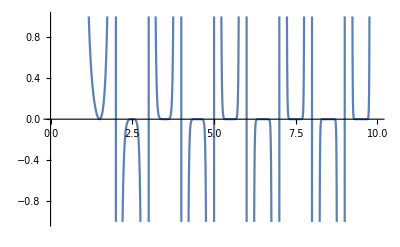

```mathematica
Plot[-(BarnesG[1/2+m1-σ1]^2 BarnesG[3/2+m1+σ1]^2)/((m1+σ1) BarnesG[m1-σ1]^2 BarnesG[m1+σ1]^2 Gamma[m1-σ1] Gamma[m1+σ1]^3)/.{m1->1},{σ1,1,10},PlotRange->{-1,1}]
```

```mathematica
((BA1[σ1+1,σ2]/.{σ2->-σ1})(BA1[σ1,σ2-1]/.{σ2->-σ1}))/((BA1[σ1+1,σ2-1]/.{σ2->-σ1})(BA1[σ1,σ2]/.{σ2->-σ1}))/.{gG->G}//Simplify
```

-(1+2 σ1)^2

```mathematica
((gG[1+m1-σ1] gG[1+m1+σ1])/(gG[1-2 σ1] gG[1+2 σ1])(gG[m1-σ1] gG[2+m1+σ1])/(gG[-1-2 σ1] gG[3+2 σ1]))^{-1}(gG[1+m1-σ1] gG[2+m1+σ1])/(gG[-2 σ1] gG[2+2 σ1])(gG[m1-σ1] gG[1+m1+σ1])/(gG[-2 σ1] gG[2+2 σ1])
```

{(gG[-1-2 σ1] gG[1-2 σ1] gG[1+2 σ1] gG[3+2 σ1])/(gG[-2 σ1]^2 gG[2+2 σ1]^2)}

```mathematica
((gG[1+m1+σ1] gG[1+m1+σ2]/.{σ1->σ1+1})(gG[1+m1+σ1] gG[1+m1+σ2]/.{σ2->σ2-1})(gG[1+m1+σ1] gG[1+m1+σ2])^(-1)(gG[1+m1+σ1] gG[1+m1+σ2]/.{σ1->σ1+1,σ2->σ2-1})^(-1)//Simplify)
```

1

```mathematica
BA1s[σ1_]:=BA1[σ1,-σ1];
(BA1s[σ1+1]BA1s[σ1-1])/(BA1s[σ1]BA1s[σ1+2])//Simplify
```

(BA1[-1+σ1,1-σ1] BA1[1+σ1,-1-σ1])/(BA1[σ1,-σ1] BA1[2+σ1,-2-σ1])

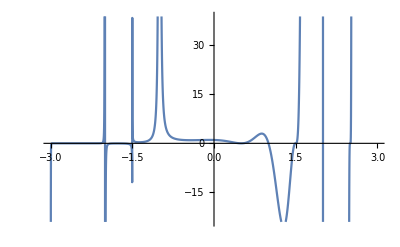

```mathematica
Plot[((1+2 σ1)^2 BarnesG[1/2+m1-σ1] BarnesG[3/2+m1-σ1] BarnesG[1/2+m1+σ1] BarnesG[3/2+m1+σ1] Gamma[2 σ1]^2)/((m1+σ1) BarnesG[m1-σ1]^2 BarnesG[m1+σ1]^2 Gamma[m1-σ1] Gamma[-2 σ1]^2 Gamma[m1+σ1]^3)/.{m1->1},{σ1,-3,3}]
```

```mathematica
Product[g[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] g[1+ToExpression[StringJoin["m",ToString[i]]]+σ2] ,{i,1,1}]/.{σ2->-σ1}
```

g[1+m1-σ1] g[1+m1+σ1]

```mathematica
σ1+1+σ2
```

```mathematica
(*the 1-loop term behaves correctly *********)
```

```mathematica
(*below is a table of instanton counting for Nf flavors*)
```

```mathematica
Nf=1;
Table[
instno=k;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Subscript[Z, k]=Sum[Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}],{i,1,Nf}]/Zbifund[σ1,σ2,Y[[1]],Y[[2]],σ1,σ2,Y[[1]],Y[[2]],0]//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}//Simplify,{k,0,3}]//Simplify
%/.{σ2->-σ1}//Simplify
```

{1,(2 m1+σ1+σ2)/(σ1-σ2)^2,(σ1^4+4 σ1 σ2+σ2^2 (-1+σ2^2)-σ1^2 (1+2 σ2^2)+m1^2 (2+4 σ1^2-8 σ1 σ2+4 σ2^2)+2 m1 (σ1+2 σ1^3+σ2-2 σ1^2 σ2-2 σ1 σ2^2+2 σ2^3))/(2 (σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2),(σ1^7-σ1^6 σ2-σ1^5 (7+3 σ2^2)+σ1^4 σ2 (11+3 σ2^2)+σ1^3 (14-4 σ2^2+3 σ2^4)+σ1^2 (10 σ2-4 σ2^3-3 σ2^5)-σ1 (8-10 σ2^2-11 σ2^4+σ2^6)+σ2 (-8+14 σ2^2-7 σ2^4+σ2^6)+4 m1^3 (12+2 σ1^4-8 σ1^3 σ2-5 σ2^2+2 σ2^4+σ1^2 (-5+12 σ2^2)+σ1 (10 σ2-8 σ2^3))+6 m1^2 (2 σ1^5-6 σ1^4 σ2+σ1^3 (-5+4 σ2^2)+σ1^2 σ2 (5+4 σ2^2)+σ1 (12+5 σ2^2-6 σ2^4)+σ2 (12-5 σ2^2+2 σ2^4))+2 m1 (-8+3 σ1^6-6 σ1^5 σ2+26 σ2^2-12 σ2^4+3 σ2^6-3 σ1^4 (4+σ2^2)+6 σ1^3 σ2 (3+2 σ2^2)+σ1^2 (26-12 σ2^2-3 σ2^4)+σ1 (20 σ2+18 σ2^3-6 σ2^5)))/(6 (σ1-σ2)^2 (1+σ1-σ2)^2 (2+σ1-σ2)^2 (1-σ1+σ2)^2 (2-σ1+σ2)^2)}

{1,m1/(2 σ1^2),(-3 σ1^2+m1^2 (1+8 σ1^2))/(4 σ1^2 (1-4 σ1^2)^2),(m1 (-1+4 σ1^2-9 σ1^4+m1^2 (3-5 σ1^2+8 σ1^4)))/(24 (σ1-5 σ1^3+4 σ1^5)^2)}

```mathematica
{1,2/(σ1-σ2)^2 t ϵ,(1+2 σ1^2-4 σ1 σ2+2 σ2^2)/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2)t^2 ϵ^2}//Total
```

1+(2 t ϵ)/(σ1-σ2)^2+(t^2 ϵ^2 (1+2 σ1^2-4 σ1 σ2+2 σ2^2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2)

```mathematica
instno =2;Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3]
```

{{{},{2}},{{},{1,1}},{{1},{1}},{{2},{}},{{1,1},{}}}

```mathematica
YoungDiagram
```

Partition::argbu: Partition called with 1 argument; between 2 and 6 arguments are expected.

Partition[{2}]

```mathematica
Sum[Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[σ2,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}],{i,1,Nf}]/Zbifund[σ1,σ2,Y[[1]],Y[[2]],σ1,σ2,Y[[1]],Y[[2]],0]//Cancel,{Y,{{{1},{1}}}}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}
```

((m1+σ1) (m1+σ2))/((-1+σ1-σ2) (1+σ1-σ2) (-1-σ1+σ2) (1-σ1+σ2))

```mathematica
((-1+m1+σ1) (m1+σ1))/(4 (-1+σ1-σ2) (σ1-σ2) (-σ1+σ2) (1-σ1+σ2))//Cancel
```

((-1+m1+σ1) (m1+σ1))/(4 (-1+σ1-σ2)^2 (σ1-σ2)^2)

```mathematica
((-1+m1+σ1) (m1+σ1))/(4 (-1+σ1-σ2)^2 (σ1-σ2)^2)//Apart
```

(-m1+m1^2-σ1+2 m1 σ1+σ1^2)/(4 (-σ1+σ2)^2)+(m1-m1^2+σ1-2 m1 σ1-σ1^2)/(2 (-σ1+σ2))+(-m1+m1^2-σ1+2 m1 σ1+σ1^2)/(4 (1-σ1+σ2)^2)+(-m1+m1^2-σ1+2 m1 σ1+σ1^2)/(2 (1-σ1+σ2))

```mathematica
(*below is the 1-instanton of tau function compared with instanton counting*)
```

```mathematica
Nf=1;
BA1[σ1_,σ2_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ2] ,{i,1,Nf}];
(BA1[σ1+1,σ2]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1+1,σ2-1])//Simplify
-((BA1[σ1+1,σ2]BA1[σ1-1,σ2])/(BA1[σ1,σ2]BA1[σ1,σ2])+(BA1[σ1,σ2+1]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1,σ2]))//Simplify
Subscript[Z, 1]/%//Simplify
```

-(1+σ1-σ2)^2

(2 m1+σ1+σ2)/(σ1-σ2)^2

1

```mathematica
-((BA1[σ1+1,σ2]BA1[σ1-1,σ2])/(BA1[σ1,σ2]BA1[σ1,σ2]))//Simplify
```

(m1+σ1)/(σ1-σ2)^2

```mathematica
(G[1+x+1]G[1+x-1])/G[1+x]^2
```

x

```mathematica
Sum[Product[ToExpression[StringJoin["σ",ToString[i]]]+ToExpression[StringJoin["m",ToString[k]]],{k,1,Nf}]/Product[If[k==i,1,(ToExpression[StringJoin["σ",ToString[i]]]-ToExpression[StringJoin["σ",ToString[k]]] )^2],{k,1,Nf}],{i,1,2}]//Simplify
```

((m1+σ1) (m2+σ1)+(m1+σ2) (m2+σ2))/(σ1-σ2)^2

```mathematica
(σ1^2+σ2^2+m2 (σ1+σ2)+m1 (2 m2+σ1+σ2))/(σ1-σ2)^2/(((m1+σ1) (m2+σ1)+(m1+σ2) (m2+σ2))/(σ1-σ2)^2)//FullSimplify
(*below is the 2-instanton of tau function compared with instanton counting*)
```

1

```mathematica
Z1loop=-((BA1[σ1+1,σ2]BA1[σ1-1,σ2])/(BA1[σ1,σ2]BA1[σ1,σ2])+(BA1[σ1,σ2+1]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1,σ2]));
Z2loop=-1/4((BA1[σ1+1,σ2]BA1[σ1-1,σ2])/(BA1[σ1,σ2]BA1[σ1,σ2])((Z1loop/.{σ1->σ1+1})+(Z1loop/.{σ1->σ1-1}))+(BA1[σ1,σ2+1]BA1[σ1,σ2-1])/(BA1[σ1,σ2]BA1[σ1,σ2])((Z1loop/.{σ2->σ2+1})+(Z1loop/.{σ2->σ2-1})))-(σ1-σ2)^2(BA1[σ1+1,σ2-1]BA1[σ1-1,σ2+1])/(BA1[σ1,σ2]BA1[σ1,σ2]);
Subscript[Z, 2]/Z2loop//Simplify
```

1

```mathematica
(BA1[σ1+1,σ2-1]BA1[σ1-1,σ2+1])/(BA1[σ1,σ2]BA1[σ1,σ2])//Cancel
```

((m1+σ1) (m1+σ2))/((-1+σ1-σ2)^2 (σ1-σ2)^4 (1+σ1-σ2)^2)

```mathematica
1/(σ1-σ2)^2(List@@(((m1+σ1) (m1+σ2))/((-1+σ1-σ2)^2 (1+σ1-σ2)^2)//Apart)//FullSimplify)
```

{((m1+σ1) (1+m1+σ1))/(4 (σ1-σ2)^2 (1+σ1-σ2)^2),(m1+σ1)^2/(4 (σ1-σ2)^2 (1+σ1-σ2)),((-1+m1+σ1) (m1+σ1))/(4 (σ1-σ2)^2 (1-σ1+σ2)^2),(m1+σ1)^2/(4 (σ1-σ2)^2 (1-σ1+σ2))}

```mathematica
{((m1+σ1) (1+m1+σ1))/(4 (σ1-σ2)^2 (1+σ1-σ2)^2),(m1+σ1)^2/(4 (σ1-σ2)^2 (1+σ1-σ2)),((-1+m1+σ1) (m1+σ1))/(4 (σ1-σ2)^2 (1-σ1+σ2)^2),(m1+σ1)^2/(4 (σ1-σ2)^2 (1-σ1+σ2))}//Total//Simplify
```

```mathematica
1/(2(1+σ1-σ2)^2)+1/(2(-1+σ1-σ2)^2)-1/((-1+σ1-σ2)^2 (1+σ1-σ2)^2)//Cancel
```

1/(2 (-1+σ1-σ2)^2)+1/(2 (1+σ1-σ2)^2)-1/((-1+σ1-σ2)^2 (1+σ1-σ2)^2)

```mathematica
1/(2x)+1/(2y)-1/(x y)//Simplify
```

(-2+x+y)/(2 x y)

```mathematica
(m1+σ1)^2/(4 (σ1-σ2)^2 (1+σ1-σ2))+(m1+σ1)^2/(4 (σ1-σ2)^2 (1-σ1+σ2))//Simplify
```

-(m1+σ1)^2/(2 (σ1-σ2)^2 (-1+σ1^2-2 σ1 σ2+σ2^2))

```mathematica
(-m1+m1^2-σ1+2 m1 σ1+σ1^2)/(4 (1-σ1+σ2)^2)//FullSimplify
```

((-1+m1+σ1) (m1+σ1))/(4 (1-σ1+σ2)^2)

```mathematica
Subscript[Z, 2]
```

(σ1^4+4 σ1 σ2+σ2^2 (-1+σ2^2)-σ1^2 (1+2 σ2^2)+m1^2 (2+4 σ1^2-8 σ1 σ2+4 σ2^2)+2 m1 (σ1+2 σ1^3+σ2-2 σ1^2 σ2-2 σ1 σ2^2+2 σ2^3))/(2 (σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2)

```mathematica
BA1[σ1_,σ2_]:=1/(G[1+σ1-σ2] G[1-σ1+σ2]) Product[G[1+ToExpression[StringJoin["m",ToString[i]]]+σ1] G[1+ToExpression[StringJoin["m",ToString[i]]]+σ2] ,{i,1,Nf}]
(BA1[σ1+1,σ2]BA1[σ1-1,σ2])/(BA1[σ1,σ2]BA1[σ1,σ2])//Cancel
```

(-m1-σ1)/(σ1-σ2)^2

```mathematica
-(σ1-σ2)^2(BA1[σ1+1,σ2-1]BA1[σ1-1,σ2+1])/(BA1[σ1,σ2]BA1[σ1,σ2])//Simplify
```

-((m1+σ1) (m1+σ2))/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2)

```mathematica
(m1+σ2)/((1+σ1-σ2) (-1-σ1+σ2))//Simplify
```

-(m1+σ2)/(1+σ1-σ2)^2

```mathematica
Γ[-1+x]/Γ[1+x]
```

1/((-1+x) x)

```mathematica
{1+σ1-σ2,1-σ1+σ2}/.{σ1->σ1-1,σ2->σ2+1}
```

{-1+σ1-σ2,3-σ1+σ2}

```mathematica
{1+δ,-1+δ}.{q1,q2}//Expand
```

q1-q2+q1 δ+q2 δ

```mathematica
Transpose[({{1+δ}, {-1+δ}})]
```

{{1+δ,-1+δ}}

```mathematica
Dot[({{1+δ}, {-1+δ}}),({{1+δ}, {-1+δ}})]
```

Dot::dotsh: Tensors {{1+δ},{-1+δ}} and {{1+δ},{-1+δ}} have incompatible shapes.

{{1+δ},{-1+δ}}.{{1+δ},{-1+δ}}

```mathematica
Transpose[({{1+δ}, {-1+δ}})].Transpose[({{1+δ}, {-1+δ}})]//Expand
```

Dot::dotsh: Tensors {{1+δ,-1+δ}} and {{1+δ,-1+δ}} have incompatible shapes.

{{1+δ,-1+δ}}.{{1+δ,-1+δ}}

```mathematica
({{1+δ}, {-1+δ}})E^({1+δ,-1+δ}.{q1[t],q2[t]})-({{1+δ}, {-1+δ}})E^(-{1+δ,-1+δ}.{q1[t],q2[t]})//MatrixForm
```

(-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (1+δ)
-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (-1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (-1+δ))

```mathematica
t D[t D[q2[t],t],t]
```

t (q2'[t]+t q2''[t])

```mathematica
DSolve[{t (q1'[t]+t q1''[t])==-t^(1/2)(-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (1+δ)),t (q2'[t]+t q2''[t])==-t^(1/2)(-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (-1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (-1+δ))},{q1[t],q2[t]},t]
```

DSolve[{t (q1'[t]+t q1''[t])==-√t (-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (1+δ)),t (q2'[t]+t q2''[t])==-√t (-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (-1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (-1+δ))},{q1[t],q2[t]},t]

```mathematica
-ⅇ^(-q2 (-1+δ)-q1 (1+δ)) (1+δ)+ⅇ^(q2 (-1+δ)+q1 (1+δ)) (1+δ)
```

```mathematica
Series[-ⅇ^(-((1+δ) q1[t])-(-1+δ) q2[t]) (1+δ)+ⅇ^((1+δ) q1[t]+(-1+δ) q2[t]) (1+δ),{δ,0,1}]
```

(ⅇ^(q1[t]-q2[t])-ⅇ^(-q1[t]+q2[t]))+(ⅇ^(-q1[t]+q2[t]) (-1+q1[t]+q2[t])+ⅇ^(q1[t]-q2[t]) (1+q1[t]+q2[t])) δ+O[δ]^2